# NLIT (Not-LIT) 9/9/21

#### set of regulator functions to smooth the discrete result of the inverse Lorentz transfrom

```mathematica
Off[Inverse::luc,General::munfl,FindFit::lstol,ClebschGordan::phy,LinearSolve::luc]
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};
SetOptions[MaTeX,"Preamble"->{"\\usepackage{color,txfonts}"}];

readREAL8list[fn_,freal_:"Real64",finteger_:"Integer32"]:=Block[{str,headmarker,data},
str=OpenRead[fn,BinaryFormat->True];
headmarker=BinaryRead[str,finteger,ByteOrdering->$ByteOrdering];
data=BinaryReadList[str,freal,ByteOrdering->$ByteOrdering];
Close[str];
data];
```

```mathematica
multipolarity=1;
mLs=Range[-multipolarity,multipolarity,1];

parity="-";
Subscript[I, n]={(*0.5,*)1.5};
J0=0.5;
mIns=Range[-#,#,1]&/@Subscript[I, n];
lege="J_lit="<>ToString[#]&/@Subscript[I, n];
thresholdLIT=(10.)^(-5);
dH=1; (* this takes only every dH basis vector into account; ECCE: not benchmarked *)
```

```mathematica
ImgSize=900;
hbarc=197.32858;
mn=938.3;
hbarsqO2m=hbarc^2/(2 mn);
αfine=1./137.;
hat[l_]:=Sqrt[2 l+1];

resultsDir="/home/kirscher/kette_repo/ComptonLIT/systems/results";

files=FileNames[All,resultsDir];
anzBas=Length[Select[files,StringMatchQ[#,"*mat*BasNR*"]&]]/Length[Subscript[I, n]];

SetDirectory[resultsDir];
dt=ToString[Import["dtype.dat"][[1]][[1]]];
datatype="Real64";
Which[dt=="float32",datatype="Real32",dt=="float64",datatype="Real64"];
Print["Read FORTRAN results from \n",Style[resultsDir,18,Red],"\nin\n",Style[dt,18,Red],"=",Style[datatype,18,Red],"\nformat for\nN_bases=",Style[anzBas,18,Red],"\nevolved bases for the expansion of the final state."];
```

Read FORTRAN results from 
/home/kirscher/kette_repo/ComptonLIT/systems/results
in
float64=Real64
format for
N_bases=4
evolved bases for the expansion of the final state.

#### Orthonormalization of the basis

the function matSqrts obtains transformation matrices to a basis whose elements correspond to the
1) orthogonal Eigenvectors of the original Norm matrix
2) barring those EVs whose Eigenvalues are smaller than the chosen threshold

```mathematica
Clear[normreg,matSqrts];

matSqrts[norm_,cutoff_:0]:=Block[{μ,transf,evs,ovsqi,ovsq,n},

{μ,transf}=Transpose[Select[Sort[Transpose[Eigensystem[norm]],#1[[1]]<#2[[1]]&],#[[1]]>cutoff&]];
evs=Eigenvalues[norm];
Print["min/max: ",MinMax[evs]];
n=Length[Select[evs,#<cutoff&]];
Print["(min/max) discarded elements: ",n," ",MinMax[Select[evs,#<cutoff&]]];
Print["elements < 0: ",Length[Select[evs,#<0.&]]];

ovsq=DiagonalMatrix[If[#<cutoff,0,Sqrt[#]]&/@evs];ovsqi=DiagonalMatrix[If[#<cutoff,0,1/Sqrt[#]]&/@evs];
(*{Drop[ovsq.es[[2]],-n],Transpose[Drop[ovsqi.es[[2]],-n]]}*)

trafma=(Transpose[transf].DiagonalMatrix[μ^(1/2)]);
invtrafma=(Transpose[transf].DiagonalMatrix[μ^(-1/2)]);
evm=(Transpose[invtrafma].norm).invtrafma;
evm=(evm+Transpose[evm])/2;(* symmetrize for stability *)
evv=Eigenvalues[evm];
Print["MinMax[Re] = ",MinMax[Re[evv]]];
Print["MinMax[Im] = ",MinMax[Im[evv]]];
(*Print[ArrayRules[SparseArray[evm]]];*)

{trafma,invtrafma}];

normreg[threshold_,norm_]:=Block[{es=Eigensystem[norm],μ,transf,μs,Or},{μ,transf}=Transpose[Select[Sort[Transpose[es],#1[[1]]<#2[[1]]&],#[[1]]>threshold&]];(Transpose[transf].DiagonalMatrix[μ^(-1/2)])];
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the initial state, i.e., J^π=(1/2)^+ for the helion

```mathematica
He3NormHamMat=readREAL8list["./mat_npp0.5^+"];
tmp=He3NormHamMat[[Range[1,Length[He3NormHamMat],2]]];
ActiveBasVHe3=ReadList["./Ssigbasv3heLIT_npp0.5^+.dat"];

BareDims=Table[ReadList["./BareBasDims_"<>ToString[nn]<>".dat"],{nn,Range[anzBas]-1}]
(*He3NormHamMat=tmp;*)
He3BasisDim=IntegerPart[Sqrt[Length[He3NormHamMat] 0.5]];
Print["N_(helion - full) = ",He3BasisDim];
Print["N_(helion - active) = ",Length[ActiveBasVHe3]];
He3Norm=ArrayReshape[He3NormHamMat[[1;;He3BasisDim^2]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
He3Ham=ArrayReshape[He3NormHamMat[[He3BasisDim^2+1;;]],{He3BasisDim,He3BasisDim}][[;;;;dH,;;;;dH]];
MinMax[Eigenvalues[He3Norm]]
```

{{369,806},{369,591},{369,619},{369,828}}

N_(helion - full) = 369

N_(helion - active) = 369

{0.0000180756,18.0514}

#### The initial state (helion ground state ^3 He ) -- in Norm-Eigen-Vector Basis

other parts of this section yield analytic information on the initial state

```mathematica
{He3Nmh,He3Nmhi}=matSqrts[He3Norm,thresholdLIT];
```

min/max: {0.0000180756,18.0514}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

B(^3He) = -4.14817

Dim_full^helion = 369=^!369   ;     Dim_(non - singular)^helion = 369

Norm=1.

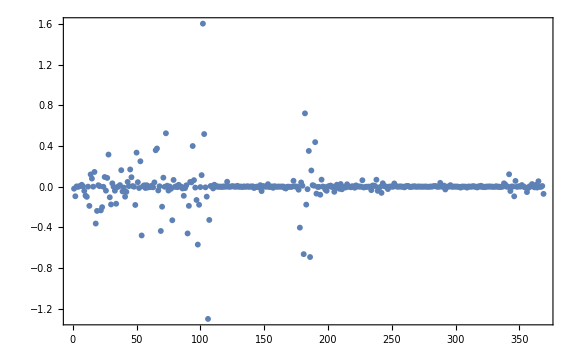
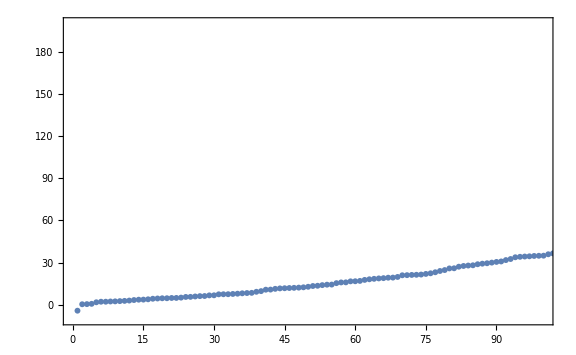
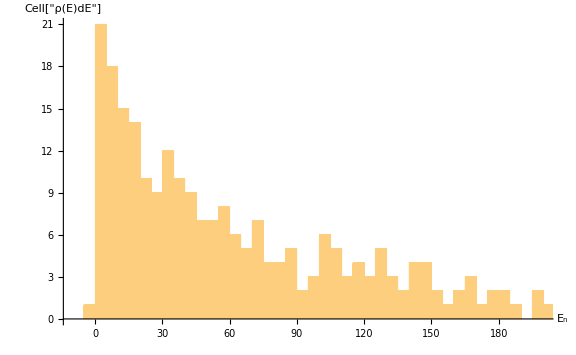
-Graphics- | 
-Graphics- | -Graphics-

```mathematica
orderedEVSYHe3=Sort[Transpose[Eigensystem[tst=Transpose[He3Nmhi].He3Ham.He3Nmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{ei,v0t}=orderedEVSYHe3[[1]];

dE=5;
Print["B(^3He) = ",ei];
Print["Dim_full^helion = ",Dimensions[He3Norm][[1]],"=^!",He3BasisDim,"   ;     Dim_(non - singular)^helion = ",Dimensions[v0t][[1]]]

fullv0=He3Nmhi.v0t;
Print["Norm=",fullv0.He3Norm.fullv0];
Grid[{{
ListPlot[Re[fullv0],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM basis vector}~n",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert {}^3\\text{He}\\right\\rangle",Magnification->2]},ImageSize->Large]},{
ListPlot[orderedEVSYHe3[[All,1]],PlotRange->{{0,100},{-10,200}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large],
Histogram[orderedEVSYHe3[[All,1]],{dE},ImageSize->Large,PlotRange->{{-10,200},Automatic},AxesLabel->{"Cell[TextData[{\n\" \",\nCell[BoxData[FormBox[\nSubscriptBox[\"E\", \"n\"], TraditionalForm]]]\n}]]","Cell[\"ρ(E)dE\"]"}]
}}]
```

### Read ⟨n|(Ĥ)_(V18+UIX)|m⟩ and ⟨n|OverHat[𝟙]|m⟩

the matrices are obtained with the FORTRAN implementation and employ normalized but non-orthogonal basis vectors.
the quantum numbers of the states m are those of the final state, i.e., J^π=(1/2)^- or J^π=(3/2)^- for the negative-parity rank-1 E_1 operator perturbing a helion;

```mathematica
matnames=FileNames["mat_*^-_BasNR-*"];
matnamesJ=Table[Select[matnames,StringMatchQ[#,"*"<>ToString[Subscript[I, n][[Inn]]]<>"*"]&],{Inn,Range[Length[Subscript[I, n]]]}];

LitNormHamMat=Table[readREAL8list[#]&/@Sort[matnamesJ[[Inn]],ToExpression[StringSplit[#1,"-"][[-1]]]<ToExpression[StringSplit[#2,"-"][[-1]]]&],{Inn,Range[Length[Subscript[I, n]]]}];

ActiveBasVFin=Table[Table[ReadList["Ssigbasv3heLIT_"<>ToString[Subscript[I, n][[Inn]]]<>"^-_BasNR-"<>ToString[nn]<>".dat"],{nn,Range[anzBas]-1}],{Inn,Range[Length[Subscript[I, n]]]}];

LITbasisDim=Table[IntegerPart[Sqrt[Length[#] 0.5]]&/@LitNormHamMat[[Inn]],{Inn,Range[Length[Subscript[I, n]]]}];

Print["N_(final - full) = ",LITbasisDim];
LitNorm=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[1;;LITbasisDim[[Inn]][[#]]^2]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];
LitHam=Table[ArrayReshape[LitNormHamMat[[Inn]][[#]][[LITbasisDim[[Inn]][[#]]^2+1;;]],{LITbasisDim[[Inn]][[#]],LITbasisDim[[Inn]][[#]]}][[;;;;dH,;;;;dH]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}];

Print["N_(final - active) = ",Length[#]&/@ActiveBasVFin];
Print["min/max Norm EV = ",Table[MinMax[Eigenvalues[LitNorm[[Inn]][[#]]]]&/@Range[anzBas],{Inn,Range[Length[Subscript[I, n]]]}]];
```

N_(final - full) = {{806,591,619,828}}

N_(final - active) = {4}

min/max Norm EV = {{{0.000179078,13.5602},{0.00208383,9.12752},{0.00157006,9.68783},{0.0000608654,14.1276}}}

#### The final state(s) (multi-pole perturbation on the helion’s ground state ^3 He ) -- in RGM Basis

```mathematica
dE=2.;
plts={};
Do[
Do[
Print["=== I_n=",Subscript[I, n][[nj]],"  BasNR: ",nb," ==="];
Print["Final-state Basis dimension = ",Dimensions[LitNorm[[nj]][[nb]]]];
{LitNmh,LitNmhi}=matSqrts[LitNorm[[nj]][[nb]],thresholdLIT];
orderedEVSYLIT=Sort[Transpose[Eigensystem[tst=Transpose[LitNmhi].LitHam[[nj]][[nb]].LitNmhi;tst=(tst+Transpose[tst])/2]],Re[#1[[1]]]<Re[#2[[1]]]&];
{eth,v0t}=orderedEVSYLIT[[1]];

v0l=LitNmhi.v0t;
Print["Norm=",v0l.LitNorm[[nj]][[nb]].v0l];
Print["lowest EV's: ",orderedEVSYLIT[[All,1]][[;;5]]];

plt1=ListPlot[Re[v0l],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert E_\\text{final}^{E_0+\\omega}\\right\\rangle",Magnification->2]},ImageSize->Large];

plt2=ListPlot[#[[1]]&/@orderedEVSYLIT,PlotRange->{{0,160},{-4,20}},Frame->True,FrameLabel->{MaTeX["n",Magnification->2],MaTeX["E_n",Magnification->2]},ImageSize->Large];
plt3=Histogram[#[[1]]&/@orderedEVSYLIT,{dE},ImageSize->Large,PlotRange->{{-10,100},Automatic},AxesLabel->{MaTeX["E_n",Magnification->2],MaTeX["\\rho(E)dE",Magnification->2]}];
AppendTo[plts,{plt1,plt2,plt3}];
Print["==="];
,{nb,Range[anzBas]}];
,{nj,Range[1,Length[Subscript[I, n]]]}];
```

=== I_n=1.5  BasNR: 1 ===

Final-state Basis dimension = {806,806}

min/max: {0.000179078,13.5602}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.89793,-1.03074,-0.340183,0.058566,0.196481}

===

=== I_n=1.5  BasNR: 2 ===

Final-state Basis dimension = {591,591}

min/max: {0.00208383,9.12752}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.0865809,0.165069,0.171941,0.190744,0.196786}

===

=== I_n=1.5  BasNR: 3 ===

Final-state Basis dimension = {619,619}

min/max: {0.00157006,9.68783}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {0.192489,0.200175,0.233623,0.295134,0.301186}

===

=== I_n=1.5  BasNR: 4 ===

Final-state Basis dimension = {828,828}

min/max: {0.0000608654,14.1276}

(min/max) discarded elements: 0 {∞,-∞}

elements < 0: 0

MinMax[Re] = {1.,1.}

MinMax[Im] = {0,0}

Norm=1.

lowest EV's: {-1.91083,-1.24747,0.0660186,0.0742002,0.114215}

===

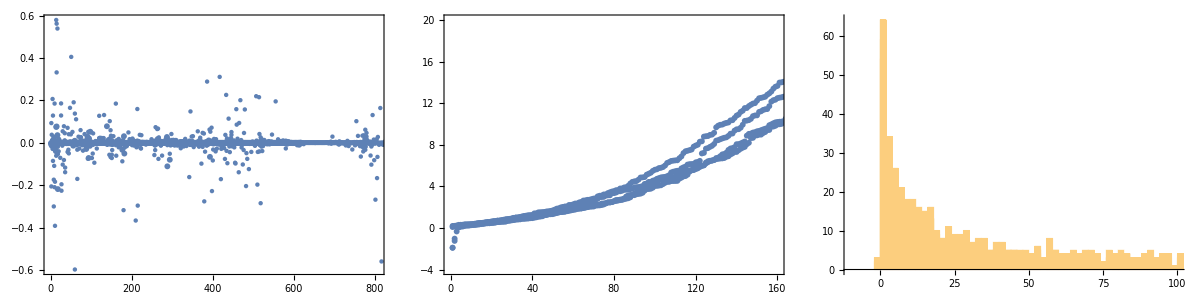

```mathematica
Grid[{{
Show[plts[[All,1]]],
Show[plts[[All,2]]],
Show[plts[[All,3]]]
}}]
```

#### Read RHS ⟨ ϕ_(lit+D3)^n|O_Lm_L|ϕ_(lit+D3)^m ⟩, n,m∈{1,N_LIT/n_k+N_D3}

the calculation is parallel in n_k parts

Normalise coupling blocks!!!!

```mathematica
CouplingBlockjs={};
CouplingBlockjAs={};

Do[
If[Sign[Subscript[I, n][[nj]]]>=0,JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],2,"0"],JLIT=StringPadRight[StringDelete[ToString[Subscript[I, n][[nj]]],"."],3,"0"]];

CouplingBlockj={};
CouplingBlockjA={};

Do[

CouplingBlock={};
CouplingBlockT={};
CouplingBlockTA={};

Do[
mM=Select[mLs,ClebschGordan[{multipolarity,#},{J0,mIn-#},{Subscript[I, n][[nj]],mIn}]≠0&];
	(*Why is mM unused here *)
fntmp = "InMIn_"<>ToString[Subscript[I, n][[nj]]]<>"_"<>ToString[mIn]<>"_BasNR-"<>ToString[nb-1]<>"."<>dt;
tmp =BinaryReadList[fntmp,datatype];

OutDim=Dimensions[tmp][[1]]/BareDims[[nb]][[1]];

test=ArrayReshape[tmp,{OutDim,BareDims[[nb]][[1]]}][[;;;;dH,;;;;dH]];
AppendTo[CouplingBlockT,{mIn,test}];
AppendTo[CouplingBlockTA,{mIn,test[[ActiveBasVFin[[nj]][[nb]],ActiveBasVHe3]]}];

,{mIn,mIns[[nj]]}];

AppendTo[CouplingBlockj,CouplingBlockT];
AppendTo[CouplingBlockjA,CouplingBlockTA];

,{nb,Range[anzBas]}];

AppendTo[CouplingBlockjs,CouplingBlockj];
AppendTo[CouplingBlockjAs,CouplingBlockjA];

,{nj,Range[1,Length[Subscript[I, n]]]}];

Print["Dim_active(⟨ψ|ο̂|helion⟩) = ",Table[Dimensions[CouplingBlockjAs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim_bare(⟨ψ|ο̂|helion⟩)   = ",Table[Dimensions[CouplingBlockjs[[Inn]][[#]][[1]][[2]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];

Print["Dim(⟨ψ|Ĥ|ψ⟩) = ",Table[Dimensions[LitHam[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
Print["Dim(⟨ψ|OverHat[1]|ψ⟩) = ",Table[Dimensions[LitNorm[[Inn]][[#]]]&/@Range[anzBas],{Inn,Range[1,Length[Subscript[I, n]]]}]];
```

Dim_active(⟨ψ|ο̂|helion⟩) = {{{806,369},{591,369},{619,369},{828,369}}}

Dim_bare(⟨ψ|ο̂|helion⟩)   = {{{806,369},{591,369},{619,369},{828,369}}}

Dim(⟨ψ|Ĥ|ψ⟩) = {{{806,806},{591,591},{619,619},{828,828}}}

Dim(⟨ψ|OverHat[1]|ψ⟩) = {{{806,806},{591,591},{619,619},{828,828}}}

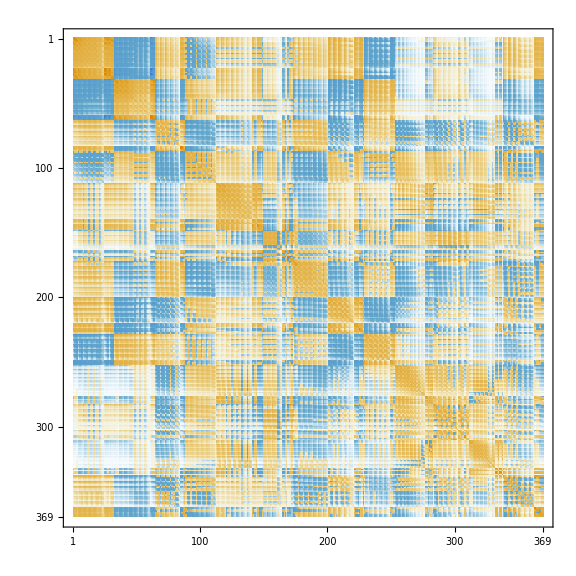
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
nb=1;nj=1;
Grid[{{
MatrixPlot[Chop[CouplingBlockjs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Coupling Matrix}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[CouplingBlockjAs[[nj]][[nb]][[1]][[2]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Optimal Coupling}",Magnification->2],ImageSize->Large]
},{
MatrixPlot[Chop[LitHam[[nj]][[nb]]],FrameLabel->{MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["E1\\otimes{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Final-state Hamiltonian}",Magnification->2],ImageSize->Large]
,
MatrixPlot[Chop[He3Ham],FrameLabel->{MaTeX["{}^3\\text{He Basis-vector}",Magnification->2],MaTeX["{}^3\\text{He Basis-vector}",Magnification->2]},PlotLabel->MaTeX["\\text{Helion Hamiltonian}",Magnification->2],ImageSize->Large]
}}]
```

#### Analysis of RHS

```mathematica
OμRHSEB=normreg[thresholdLIT,He3Norm];
tmp=(Transpose[OμRHSEB].He3Ham).OμRHSEB; tmp=(tmp+Transpose[tmp])/2;
{λsHeEB,trfHeEB}=Eigensystem[tmp];
evgsEB=Flatten[trfHeEB[[TakeSmallest[λsHeEB->"Index",1]]]];
inhomoEB={};evgsEB=OμRHSEB.evgsEB;
Print["ev=",TakeSmallest[λsHeEB,1][[1]]," norm=",evgsEB.He3Norm.evgsEB];
```

ev=-4.14817 norm=1.

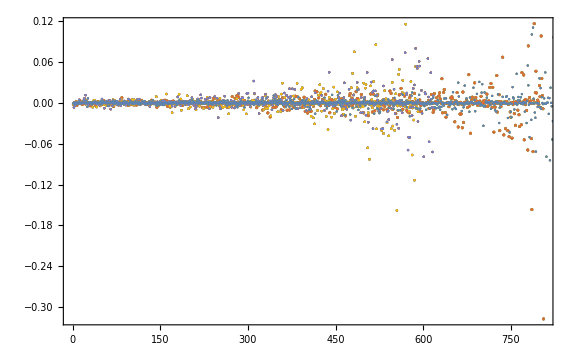

```mathematica
inhomoEB=Table[{},{nj,Length[Subscript[I, n]]}];
pltss={};
Do[
Do[
OμLHSEB=normreg[thresholdLIT,LitNorm[[nj]][[nb]]];
tmp=(Transpose[OμLHSEB].LitHam[[nj]][[nb]]).OμLHSEB;
tmp=(tmp+Transpose[tmp])/2;
{λfinalEB,trfLitEB}=Eigensystem[tmp];
Do[
tmp=CouplingBlockjAs[[nj]][[nb]][[mm]][[2]];
AppendTo[inhomoEB[[nj]],Transpose[OμLHSEB].(tmp.evgsEB)];
,{mm,Range[1,Length[mIns[[nj]]]]}
];AppendTo[pltss,ListPlot[inhomoEB[[nj]],PlotRange->Full,Frame->True,FrameLabel->{MaTeX["\\text{RGM Basis-vector}~\\left\\vert n\\right\\rangle",Magnification->2],MaTeX["\\left\\langle n\\Big\\vert O\\Big\\vert \\text{He}3 \\right\\rangle",Magnification->2]},ImageSize->Large]];
,{nb,Range[anzBas]}
];
,{nj,Range[1,Length[Subscript[I, n]]]}
];
Show[pltss]
```

#### “algebraic” LIT (norm zero-mode removal)

L_ν'L'νL^(I_f I_i;I_n)(k,k;σ)=(-)^(I_n-I_i+L-L'+ν')ρ(I_n,σ)∑_M_n ⟨ψ_(I_f I_i M_n)^ν'L'(k,σ)|ψ_(I_f I_i M_n)^νL(k,σ)⟩

#### Direct calculation of the (partial) strength functions

F_ν'L'νL^(I_f I_i)(k,k;E)=ρ(I_n,E) · ⟨I_f E_f||M^ν'L'(k')||I_n E ⟩⟨I_n E||M^(⋁L)(k)||I_i E_i ⟩
⇒ ρ(I_n,E)∝θ(E-E_i-k)

```mathematica
lpsisEV={};CumStrengthsEV={};

{μEV,transfEV}=Transpose[Select[Sort[Transpose[Eigensystem[He3Norm]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμRHSEV=(Transpose[transfEV].DiagonalMatrix[μEV^(-1/2)]);

{EvalsIEV,EvecsIEV}=Eigensystem[tmp=(Transpose[OμRHSEV].He3Ham).OμRHSEV;(tmp+Transpose[tmp])/2];
EvecGSiEV=OμRHSEV.Flatten[EvecsIEV[[TakeSmallest[EvalsIEV->"Index",1]]]];
EvalGSiEV=Min[EvalsIEV];
EvalGSiEV
{EvecGSiEV.He3Norm.EvecGSiEV,EvecGSiEV.He3Ham.EvecGSiEV}
```

-4.14817

{1.,-4.14817}

```mathematica
CumStrengthsJ={};pltsssJ={};
Do[
CumStrengths={};pltsss={};
Print[" J_final = ",Subscript[I, n][[nj]]];
Print["E_0^initial = ",EvalGSiEV,"    dim = ",Dimensions[EvalsIEV]];
Do[

{μlEV,transflEV}=Transpose[Select[Sort[Transpose[Eigensystem[LitNorm[[nj]][[nb]]]],#1[[1]]<#2[[1]]&],#[[1]]>thresholdLIT&]];
OμLHSEV=(Transpose[transflEV].DiagonalMatrix[μlEV^(-1/2)]);

{EvalsFEV,EvecsFEV}=Eigensystem[tmp=(Transpose[OμLHSEV].(LitHam[[nj]][[nb]])).OμLHSEV;(tmp+Transpose[tmp])/2];
{EvalsFEV,EvecsFEV}=Sort[{EvalsFEV,EvecsFEV},#1[[1]]<#2[[1]]&];
EvecGSfEV=OμLHSEV.Flatten[EvecsFEV[[TakeSmallest[EvalsFEV->"Index",1]]]];
EvalGSfEV=Min[EvalsFEV];

Print["Basisensemble ",nb,":  E_0^final  = ",EvalGSfEV,"    dim   = ",Dimensions[EvalsFEV]];
tmplEV=0;

Do[
inhomoEV=Transpose[OμLHSEV].(CouplingBlockjAs[[nj]][[nb]][[mm]][[2]].EvecGSiEV);

tmplEV=tmplEV+(EvecsFEV.inhomoEV)^2;
,{mm,Length[mIns[[nj]]]}
];
lpsisEV=Transpose[{EvalsFEV,tmplEV}];

CumStrengthsEV=Transpose[{Sort[lpsisEV][[All,1]],Accumulate[Sort[lpsisEV][[All,2]]]}];

pl1=
ListPlot[lpsisEV,Joined->False,PlotMarkers->{{♔,12},{♗,12}},PlotRange->{{-3,7.5},{0,Automatic}},Filling->Axis,FillingStyle->{{Blue},{Red}},PlotRange->{Full,Full},AxesLabel->{MaTeX["\\text{E~[MeV]}",Magnification->2],MaTeX["\\left\\langle J^\\pi_{E_n=\\omega_\\text{lab}-E_0}\\Big\\vert\\widehat{E1}\\Big\\vert\\left({}^3\\text{He}\\right)_{E_0}^{1/2^+}\\right\\rangle^2",Magnification->2]},ImageSize->ImgSize];
pl2=
ListPlot[CumStrengthsEV,Joined->False,ImageSize->ImgSize,PlotRange->{{-3,350},{0,Automatic}},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->2],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->2]},PlotLabel->MaTeX["\\text{EV order}",Magnification->2]];

AppendTo[pltsss,{pl1,pl2}];
AppendTo[CumStrengths,CumStrengthsEV];

,{nb,Range[anzBas]}
];
AppendTo[pltsssJ,pltsss];
AppendTo[CumStrengthsJ,CumStrengths];
,{nj,Range[1,Length[Subscript[I, n]]]}
]
```

J_final = 1.5

E_0^initial = -4.14817    dim = {369}

Basisensemble 1:  E_0^final  = -1.89793    dim   = {806}

Basisensemble 2:  E_0^final  = 0.0865809    dim   = {591}

Basisensemble 3:  E_0^final  = 0.192489    dim   = {619}

Basisensemble 4:  E_0^final  = -1.91083    dim   = {828}

```mathematica
Integrate[8 Pi^2 x^2 (x Exp[-x^2/(4 α)-(ω-0.75 x^2)/α]/(3 Pi^1.5 α^2.5))^2/(2 √(ω-0.75 x^2)),{x,0,√(4. ω/3.)},Assumptions->{α∈Reals,α>0,ω∈Reals,ω>0}];

NielsF[ω_,α_]:=(ⅇ^(-(4 ω)/(3 α)) ((ω/α)^2 BesselI[0,(2 ω)/(3 α)]+((ω/α)^2-3 ω/α) BesselI[1,(2 ω)/(3 α)]))/(81 √3 α^2);
NielsC[λ_,α_]:=NIntegrate[NielsF[ω,α],{ω,0,λ}]

emin=-3;emax=1250;
sc=0.975 (4 Pi/137)^-1;
αRGM=1.8;

CumStrengthsJwithD={};
FittedCum={};FittedCum2={};
StrengthF={};StrengthF2={};
listplots={};
mn=0.000001;

basIndices=Range[anzBas];

Do[
Clear[a,b,c,a2,b2,c2,d2];
(* exclude sets with no strength below "strengthTH" *)
strengthTH=-10;
cleanSet=Flatten[Select[Sort[CumStrengthsJ[[nj]][[basIndices]]],#[[1]][[1]]>strengthTH&],1];
offset=Min[cleanSet[[All,1]]];
fitSetShifted=Chop[Transpose[{cleanSet[[All,1]]-offset,cleanSet[[All,2]]}]];
ffun=(b(x+mn)^a)/(1+c(x+mn)^a);
ffun2=(b2(x+mn)^a2)/(1+d2(x+mn)^(a2/2)+c2(x+mn)^a2);
rr=FindFit[fitSetShifted,ffun,{a,b,c},x];
rr2=FindFit[fitSetShifted,ffun2,{a2,b2,c2,d2},x];
AppendTo[CumStrengthsJwithD,cleanSet];
AppendTo[FittedCum,ffun/.rr/.x->e-offset];
AppendTo[StrengthF,D[FittedCum[[-1]],e]];
AppendTo[FittedCum2,ffun2/.rr2/.x->e-offset];
AppendTo[StrengthF2,D[FittedCum2[[-1]],e]];
Do[
AppendTo[listplots,
ListPlot[CumStrengthsJ[[nj]][[basSet]],Joined->False,ImageSize->ImgSize,PlotRange->{{emin,emax},Full},AxesLabel->{MaTeX["E~\\left[\\text{MeV}\\right]",Magnification->1],MaTeX["\\int_{-\\infty}^EF~\\left[\\text{??}\\right]",Magnification->1]},PlotLabel->MaTeX["",Magnification->2],ImageSize->Large,PlotStyle->Directive[ColorData[12][4 basSet],PointSize[0.005]],PlotLegends->"J_final^(π = -) = "<>ToString[Subscript[I, n][[nj]]]]];
,{basSet,basIndices}];
,{nj,Range[Length[Subscript[I, n]]]}];

plotDat=Show[listplots];
plotDatFit=Show[
plotDat,
Plot[FittedCum,{e,emin,emax},PlotRange->All,PlotStyle->{{Orange,Dashed,Thickness[0.005],Opacity[0.25]},{Green,Dotted,Thickness[0.005]}}],Plot[FittedCum2,{e,emin,emax},PlotRange->All,PlotStyle->{{Blue,Dashed,Thickness[0.0025],Opacity[0.5]},{White,Thickness[0.0025]}}]
,ImageSize->ImgSize];

Export[resultsDir<>"/tmp.pdf",plotDatFit];
(*,
Plot[sc NielsC[λ/hbarsqO2m,αRGM]/fl,{λ,emin,emax},PlotRange->{{emin,emax},Automatic},PlotStyle->{Magenta,Thick},ImageSize->Large]*)

Put[CumStrengthsJwithD,LocalObject["CumStr_05_15"]]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

LocalObject[file:///home/kirscher/.Wolfram/Objects/CumStr_05_15]

[σ_tot]=μb=10^-4 fm^2
[σ_tot]=mb=10^-1 fm^2
[Lab photon energy] = MeV

dipole calculation from B. Gibson & D.R. Lehmann, PRC 13,2 (1976) (T=3/2 only!)
and Golak et al.

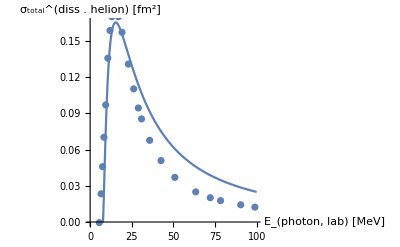

```mathematica
He3DatamBarnGolak=Import["../data/he3_photo_diss_sigma_golak.dat","Data"];
He3DatamBarnGibson=Import["../data/he3_photo_diss_sigma_gibson.dat","Data"];Bhe=7.67;
He3DataFm2=Transpose[{Transpose[He3DatamBarnGolak][[1]],Transpose[He3DatamBarnGolak][[2]] 10.^(-1)}];

σBethe[ω_,E0_,mM_]:=4 (8 Pi)/3 1./137. 1./(mM E0) (ω/E0-1)^(3./2.)/(ω/E0)^3;
Show[
Plot[hbarc^2 σBethe[ν,Bhe,938.],{ν,0,100},PlotRange->Full,AxesLabel->{"E_(photon, lab) [MeV]","σ_total^(diss . helion) [fm^2]"}],
ListPlot[He3DataFm2,PlotLabel->Style["Gibson - E1",Orange,22]]]
```

#### σ_tot=(2π)^2 α·E_γ ∑_(J,M) JM OverHat[E1](J_0 m_0)^2

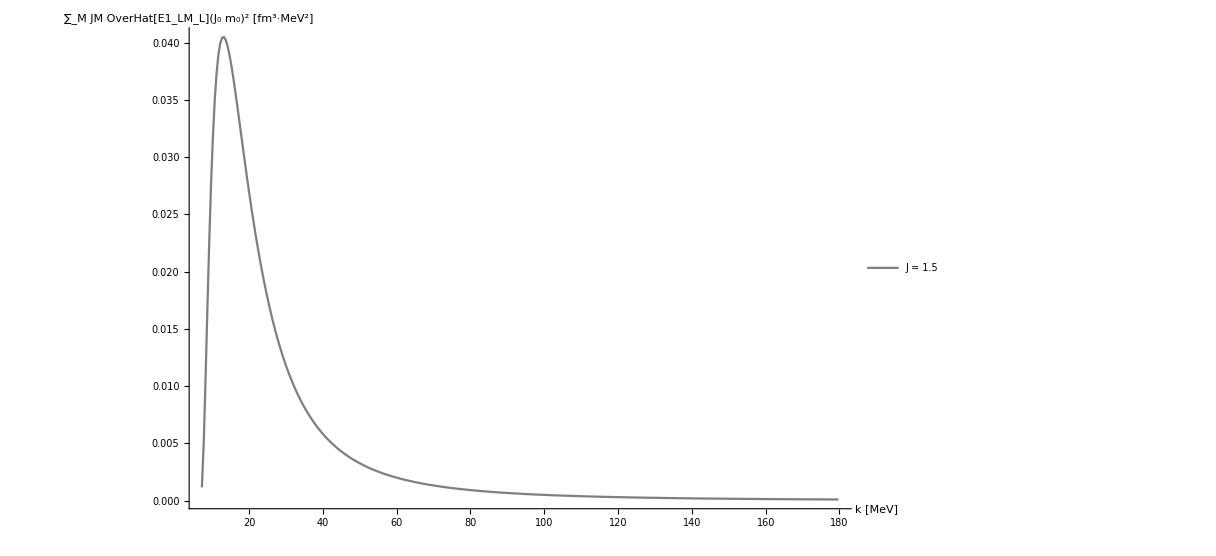
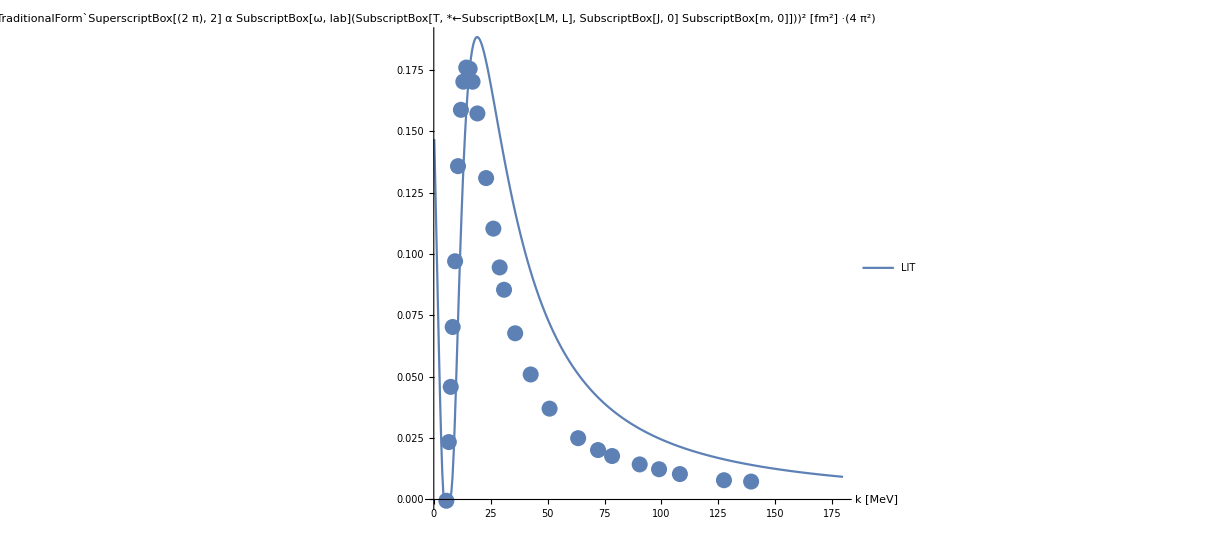
-Graphics- | -Graphics-

```mathematica
Clear[ee,e2];
k0=0.001;k1=180;dK=0.5;
Subscript[k, lab]=Range[Abs[eth],k1,dK];
Ji=Jf=J0;Mi=Ji;Mf=Mi;

labelj=("J = "<>ToString[#])&/@Subscript[I, n];

strengthfunctionList=Table[Table[(StrengthF2[[nJ]]/.e->ee)/.ee->(ei+kmag),{kmag,Subscript[k, lab]}],{nJ,Range[1,Length[Subscript[I, n]]]}];

z=List[];

For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,(
atmp=ListLinePlot[strengthfunctionList[[nJ,All]],PlotRange->Full,LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","FormBox[RowBox[{UnderscriptBox[\"∑\", \"M\"], RowBox[{TemplateBox[{\"JM\"},\"Bra\"], OverscriptBox[SubscriptBox[\"E1\", SubscriptBox[\"LM\", \"L\"]], \"^\"], SuperscriptBox[TemplateBox[{RowBox[{SubscriptBox[\"J\", \"0\"], SubscriptBox[\"m\", \"0\"]}]},\"Ket\"], \"2\"]}]}],TraditionalForm] [fm^3·MeV^2]"},ImageSize->ImgSize,Joined->True,DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotStyle->{ColorData[7,"ColorList"][[nJ]]},PlotLegends->{labelj[[nJ]]}];
AppendTo[z,atmp];
)];

Tsquared[Mf_,Mi_,λf_,θ_]:=
Module[{compo},
ampli=0;
For[nJ=1,nJ≤Length[Subscript[I, n]],nJ++,
compo=strengthfunctionList[[nJ,All]];
For[Mm=-multipolarity,Mm≤multipolarity,Mm++,
For[Mmp=-multipolarity,Mmp≤multipolarity,Mmp++,
ampli+=compo;
];
];];
Return[ampli]
]
fudgi=(2 π)^2;

kinfac=fudgi (2 Pi)^2 αfine (Subscript[k, lab]+ei)/hbarc;

DissCross[Mf_,Mi_,λf_,kinfac_]:=kinfac Tsquared[Mf,Mi,λf,θ];
lf=1;

Grid[{{
Show[z,PlotRange->All],
Show[ListPlot[Re[DissCross[Jf,Ji,lf,kinfac]],PlotRange->{Automatic,{0,Full}},LabelStyle->Directive[Larger],AxesLabel->{"k [MeV]","(TraditionalForm`SuperscriptBox[(2  π), 2] α SubscriptBox[ω, lab](SubscriptBox[T, *←SubscriptBox[LM, L], SubscriptBox[J, 0] SubscriptBox[m, 0]]))^2 [fm^2] ·("<>ToString[Style[fudgi,Red],TraditionalForm]<>")"}(*,Filling->cycl*),ImageSize->ImgSize,Joined->{True,False},DataRange->{Min[Subscript[k, lab]],Max[Subscript[k, lab]]},PlotLegends->{"LIT"}],ListPlot[He3DataFm2,PlotLegends->"σ_tot data"]
]
}}]
```

d^5 σ_(He→npp)=(2π)^2 α ω_lab ∑|p_1 q_1Ô(ω)He|^2 d^3(p_1,q_1)δ(p_1^2+3/4 q_1^2-ω)

```mathematica
Clear[solu,wcm,wlab,wcem]
solu=Solve[wcm==wlab (1+2 wlab/mdeu)^(-1/2),wlab];
wl=Simplify[wlab/.solu[[2]]]

kcross=0.5 Sqrt[(wcem+e0-2 mn)(wcem+e0+2 mn)]
```

(wcm^2+√(wcm^2 (mdeu^2+wcm^2)))/mdeu

0.5 √((-2.×10^-6+e0+wcem) (2.×10^-6+e0+wcem))